### Sub-expressions

```mathematica
Clear["Global`*"]
```

```mathematica
subExpression[expr_] :=
	Cases[expr,_,{0,Infinity}];
```

```mathematica
expr0=f[g[h]];
list=subExpression[expr0]
```

{h,g[h],f[g[h]]}

```mathematica
tree0=expr0//ExpressionTree
tree0//TreeCases[_]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
exprlist={a,b};
rulelist=Outer[Rule,list,exprlist]//Flatten
```

{h→a,h→b,g[h]→a,g[h]→b,f[g[h]]→a,f[g[h]]→b}

```mathematica
Replace[expr0,#,{0,Infinity}]&/@rulelist
```

{f[g[a]],f[g[b]],f[a],f[b],a,b}

```mathematica
Replace[expr0,g->a,{0,Infinity},Heads->False]
Replace[expr0,g->a,{0,Infinity},Heads->True]
```

f[g[h]]

f[a[h]]

```mathematica
Replace[expr0,f[g]->a,{0,Infinity},Heads->True]
Replace[expr0,f[g[x_]]:>a[x],{0,Infinity}]
```

f[g[h]]

a[h]

### TreeForm

The functions TF and exportSVG are in lilyric`.

-Graphics-

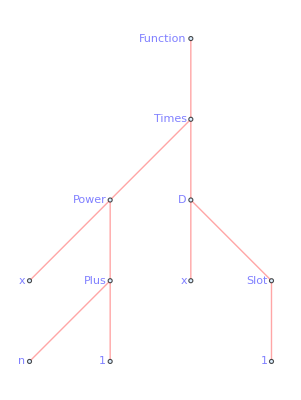

```mathematica
L[n_]:=(x^(n+1) D[#,x])&;

L[n]//ExpressionTree
L[n]//TF[]//exportSVG["tree-example-Witt"]
```

$RecursionLimit::reclim2: Recursion depth of 20 exceeded during evaluation of -f.

{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f}}}}}}}}}}}}}}}}}

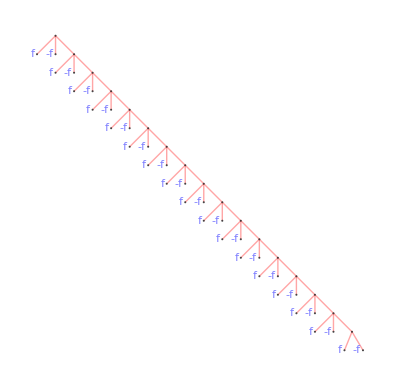

```mathematica
Clear[f]
divergence=Block[{$RecursionLimit=20,f},
	f:=-f;
	Trace[f,f]
]/.{-f->"-f"}//ReleaseHold

divergence//TF[List]//exportSVG["trace-1"]
```

### Non-standard evaluation

```mathematica
f=g;
subExpression[f[1+1]]
```

{2,g[2]}

```mathematica
subExpressionHold//Attributes={HoldFirst};
subExpressionHold[expr_,wrapper_:HoldForm,opts:OptionsPattern[]]:=
    Cases[Unevaluated@expr,
        subexpr_:>wrapper@subexpr,
        {0,Infinity},
        FilterRules[{opts},Options[Cases]],
        Heads->False
    ];
```

```mathematica
subExpressionHold[f[1+1]]
```

{1,1,1+1,f[1+1]}

```mathematica
Names["System`*Hold*"]
```

{Hold,HoldAll,HoldAllComplete,HoldComplete,HoldFirst,HoldForm,HoldPattern,HoldRest,NHoldAll,NHoldFirst,NHoldRest,ReleaseHold,SequenceHold,$ConditionHold}

```mathematica
Names["System`*active*",IgnoreCase->True]
```

{Active,ActiveClassification,ActiveClassificationObject,ActiveItem,ActivePrediction,ActivePredictionObject,ActiveStyle,ControlActive,IgnoringInactive,Inactive,InactiveStyle,Interactive,InteractiveTradingChart,ScheduledTaskActiveQ,$ControlActiveSetting}

```mathematica
Clear["Global`*"]
```